## Tutorial-Examples for the SymmetricFunctions Package

## I. Loading package

```mathematica
<<SymmetricFunctions`
```

------------------------------------------------------------

SymmetricFunctions  version 1.0.0, {2023,24,2}

Copyright (C) 2020-2022, Thomas Helpin, under the General Public License.

```mathematica
Names["SymmetricFunctions`*"]
```

{BranchingRule,BratteliDiagramSn,BratteliPathSn,ChangeSymmetricBasis,CharacterSymmetricGroup,CompleteSymmetricFunction,CompleteSymmetricPolynomial,DimOfIrrep,DimOfIrrepSn,Disclaimer,ElementarySymmetricFunction,ElementarySymmetricPolynomial,GeneralLinearGroup,IncludedPartitionQ,InverseKostkaCoefficient,InverseLittlewoodRichardsonRule,KostkaCoefficient,LittlewoodRichardsonCoefficient,LittlewoodRichardsonRule,LittlewoodRichardsonTableaux,MonomialSymmetricFunction,MonomialSymmetricPolynomial,NewellLittlewoodCoefficient,NewellLittlewoodRule,OrthogonalGroup,Output,PartitionDominatesQ,PartitionJoin,PartitionMultiplicities,Plethysm,PowerSymmetricFunction,SchurFunction,SchurPolynomial,SemiStandardTableaux,StandardTableaux,SymmetricFunctionBasis,SymmetricFunctionExpand,SymmetricFunctionQ,SymplecticGroup,TableauForm,ToPolynomial,TransposePartition,ZCoefficient,$LieGroups,$SymmetricFunctions,$Version}

## II. Standard symmetric functions

### 1. Symmetric functions and change of basis

```mathematica
$SymmetricFunctions
```

{ElementarySymmetricFunction,MonomialSymmetricFunction,CompleteSymmetricFunction,PowerSymmetricFunction,SchurFunction}

```mathematica
?SymmetricFunctionQ
```

```mathematica
?SymmetricFunctionExpand
```

```mathematica
?ChangeSymmetricBasis
```

#### a. Elementary Symmetric functions

```mathematica
ElementarySymmetricFunction[6]*ElementarySymmetricFunction[4]
ElementarySymmetricFunction[{6,4}]
ElementarySymmetricFunction[{2,1}]*ElementarySymmetricFunction[{2,1}]*ElementarySymmetricFunction[{6}]
```

(ē)_{6,4}

(ē)_{6,4}

(ē)_{6,2,2,1,1}

```mathematica
ElementarySymmetricFunction[{4,2,1}]*ElementarySymmetricFunction[{3,2,1}]+ElementarySymmetricFunction[{4,2,1}]*ElementarySymmetricFunction[{2,1}]
```

(ē)_{4,2,2,1,1}+(ē)_{4,3,2,2,1,1}

```mathematica
(******** Change of Basis *********)
```

```mathematica
ElementarySymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,CompleteSymmetricFunction]
ChangeSymmetricBasis[%,ElementarySymmetricFunction]
```

(ē)_{4,2,1}

(h̄)_{4,2,1}-(h̄)_{2,2,2,1}-2 (h̄)_{3,2,1,1}-(h̄)_{4,1,1,1}+4 (h̄)_{2,2,1,1,1}+2 (h̄)_{3,1,1,1,1}-4 (h̄)_{2,1,1,1,1,1}+(h̄)_{1,1,1,1,1,1,1}

(ē)_{4,2,1}

```mathematica
ElementarySymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,PowerSymmetricFunction]
ChangeSymmetricBasis[%,ElementarySymmetricFunction]
```

(ē)_{4,2,1}

1/8 (p̄)_{4,2,1}-1/16 (p̄)_{2,2,2,1}-1/6 (p̄)_{3,2,1,1}-1/8 (p̄)_{4,1,1,1}+3/16 (p̄)_{2,2,1,1,1}+1/6 (p̄)_{3,1,1,1,1}-7/48 (p̄)_{2,1,1,1,1,1}+1/48 (p̄)_{1,1,1,1,1,1,1}

(ē)_{4,2,1}

```mathematica
PowerSymmetricFunction[#]&/@IntegerPartitions[8]
RepeatedTiming[ChangeSymmetricBasis[%,MonomialSymmetricFunction]]
```

{(p̄)_{8},(p̄)_{7,1},(p̄)_{6,2},(p̄)_{6,1,1},(p̄)_{5,3},(p̄)_{5,2,1},(p̄)_{5,1,1,1},(p̄)_{4,4},(p̄)_{4,3,1},(p̄)_{4,2,2},(p̄)_{4,2,1,1},(p̄)_{4,1,1,1,1},(p̄)_{3,3,2},(p̄)_{3,3,1,1},(p̄)_{3,2,2,1},(p̄)_{3,2,1,1,1},(p̄)_{3,1,1,1,1,1},(p̄)_{2,2,2,2},(p̄)_{2,2,2,1,1},(p̄)_{2,2,1,1,1,1},(p̄)_{2,1,1,1,1,1,1},(p̄)_{1,1,1,1,1,1,1,1}}

{0.00379966,{(m̄)_{8},(m̄)_{8}+(m̄)_{7,1},(m̄)_{8}+(m̄)_{6,2},(m̄)_{8}+(m̄)_{6,2}+2 (m̄)_{7,1}+2 (m̄)_{6,1,1},(m̄)_{8}+(m̄)_{5,3},(m̄)_{8}+(m̄)_{5,3}+(m̄)_{6,2}+(m̄)_{7,1}+(m̄)_{5,2,1},(m̄)_{8}+(m̄)_{5,3}+3 (m̄)_{6,2}+3 (m̄)_{7,1}+3 (m̄)_{5,2,1}+6 (m̄)_{6,1,1}+6 (m̄)_{5,1,1,1},(m̄)_{8}+2 (m̄)_{4,4},(m̄)_{8}+2 (m̄)_{4,4}+(m̄)_{5,3}+(m̄)_{7,1}+(m̄)_{4,3,1},(m̄)_{8}+2 (m̄)_{4,4}+2 (m̄)_{6,2}+2 (m̄)_{4,2,2},(m̄)_{8}+2 (m̄)_{4,4}+2 (m̄)_{5,3}+2 (m̄)_{6,2}+2 (m̄)_{7,1}+2 (m̄)_{4,2,2}+2 (m̄)_{4,3,1}+2 (m̄)_{5,2,1}+2 (m̄)_{6,1,1}+2 (m̄)_{4,2,1,1},(m̄)_{8}+2 (m̄)_{4,4}+4 (m̄)_{5,3}+6 (m̄)_{6,2}+4 (m̄)_{7,1}+6 (m̄)_{4,2,2}+4 (m̄)_{4,3,1}+12 (m̄)_{5,2,1}+12 (m̄)_{6,1,1}+12 (m̄)_{4,2,1,1}+24 (m̄)_{5,1,1,1}+24 (m̄)_{4,1,1,1,1},(m̄)_{8}+2 (m̄)_{5,3}+(m̄)_{6,2}+2 (m̄)_{3,3,2},(m̄)_{8}+4 (m̄)_{4,4}+2 (m̄)_{5,3}+(m̄)_{6,2}+2 (m̄)_{7,1}+2 (m̄)_{3,3,2}+4 (m̄)_{4,3,1}+2 (m̄)_{6,1,1}+4 (m̄)_{3,3,1,1},(m̄)_{8}+2 (m̄)_{4,4}+3 (m̄)_{5,3}+2 (m̄)_{6,2}+(m̄)_{7,1}+4 (m̄)_{3,3,2}+2 (m̄)_{4,2,2}+(m̄)_{4,3,1}+2 (m̄)_{5,2,1}+2 (m̄)_{3,2,2,1},(m̄)_{8}+6 (m̄)_{4,4}+5 (m̄)_{5,3}+4 (m̄)_{6,2}+3 (m̄)_{7,1}+8 (m̄)_{3,3,2}+6 (m̄)_{4,2,2}+9 (m̄)_{4,3,1}+6 (m̄)_{5,2,1}+6 (m̄)_{6,1,1}+6 (m̄)_{3,2,2,1}+12 (m̄)_{3,3,1,1}+6 (m̄)_{4,2,1,1}+6 (m̄)_{5,1,1,1}+6 (m̄)_{3,2,1,1,1},(m̄)_{8}+10 (m̄)_{4,4}+11 (m̄)_{5,3}+10 (m̄)_{6,2}+5 (m̄)_{7,1}+20 (m̄)_{3,3,2}+30 (m̄)_{4,2,2}+25 (m̄)_{4,3,1}+30 (m̄)_{5,2,1}+20 (m̄)_{6,1,1}+30 (m̄)_{3,2,2,1}+40 (m̄)_{3,3,1,1}+60 (m̄)_{4,2,1,1}+60 (m̄)_{5,1,1,1}+60 (m̄)_{3,2,1,1,1}+120 (m̄)_{4,1,1,1,1}+120 (m̄)_{3,1,1,1,1,1},(m̄)_{8}+6 (m̄)_{4,4}+4 (m̄)_{6,2}+12 (m̄)_{4,2,2}+24 (m̄)_{2,2,2,2},(m̄)_{8}+6 (m̄)_{4,4}+6 (m̄)_{5,3}+4 (m̄)_{6,2}+2 (m̄)_{7,1}+12 (m̄)_{3,3,2}+12 (m̄)_{4,2,2}+6 (m̄)_{4,3,1}+6 (m̄)_{5,2,1}+2 (m̄)_{6,1,1}+24 (m̄)_{2,2,2,2}+12 (m̄)_{3,2,2,1}+6 (m̄)_{4,2,1,1}+12 (m̄)_{2,2,2,1,1},(m̄)_{8}+14 (m̄)_{4,4}+12 (m̄)_{5,3}+8 (m̄)_{6,2}+4 (m̄)_{7,1}+40 (m̄)_{3,3,2}+32 (m̄)_{4,2,2}+28 (m̄)_{4,3,1}+20 (m̄)_{5,2,1}+12 (m̄)_{6,1,1}+72 (m̄)_{2,2,2,2}+56 (m̄)_{3,2,2,1}+48 (m̄)_{3,3,1,1}+36 (m̄)_{4,2,1,1}+24 (m̄)_{5,1,1,1}+72 (m̄)_{2,2,2,1,1}+48 (m̄)_{3,2,1,1,1}+24 (m̄)_{4,1,1,1,1}+48 (m̄)_{2,2,1,1,1,1},(m̄)_{8}+30 (m̄)_{4,4}+26 (m̄)_{5,3}+16 (m̄)_{6,2}+6 (m̄)_{7,1}+140 (m̄)_{3,3,2}+120 (m̄)_{4,2,2}+90 (m̄)_{4,3,1}+66 (m̄)_{5,2,1}+30 (m̄)_{6,1,1}+360 (m̄)_{2,2,2,2}+300 (m̄)_{3,2,2,1}+240 (m̄)_{3,3,1,1}+210 (m̄)_{4,2,1,1}+120 (m̄)_{5,1,1,1}+540 (m̄)_{2,2,2,1,1}+480 (m̄)_{3,2,1,1,1}+360 (m̄)_{4,1,1,1,1}+720 (m̄)_{2,2,1,1,1,1}+720 (m̄)_{3,1,1,1,1,1}+720 (m̄)_{2,1,1,1,1,1,1},(m̄)_{8}+70 (m̄)_{4,4}+56 (m̄)_{5,3}+28 (m̄)_{6,2}+8 (m̄)_{7,1}+560 (m̄)_{3,3,2}+420 (m̄)_{4,2,2}+280 (m̄)_{4,3,1}+168 (m̄)_{5,2,1}+56 (m̄)_{6,1,1}+2520 (m̄)_{2,2,2,2}+1680 (m̄)_{3,2,2,1}+1120 (m̄)_{3,3,1,1}+840 (m̄)_{4,2,1,1}+336 (m̄)_{5,1,1,1}+5040 (m̄)_{2,2,2,1,1}+3360 (m̄)_{3,2,1,1,1}+1680 (m̄)_{4,1,1,1,1}+10080 (m̄)_{2,2,1,1,1,1}+6720 (m̄)_{3,1,1,1,1,1}+20160 (m̄)_{2,1,1,1,1,1,1}+40320 (m̄)_{1,1,1,1,1,1,1,1}}}

```mathematica
ElementarySymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,MonomialSymmetricFunction]
ChangeSymmetricBasis[%,ElementarySymmetricFunction]
```

(ē)_{4,2,1}

3 (m̄)_{2,2,2,1}+(m̄)_{3,2,1,1}+11 (m̄)_{2,2,1,1,1}+4 (m̄)_{3,1,1,1,1}+35 (m̄)_{2,1,1,1,1,1}+105 (m̄)_{1,1,1,1,1,1,1}

(ē)_{4,2,1}

```mathematica
ElementarySymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,SchurFunction]
ChangeSymmetricBasis[%,ElementarySymmetricFunction]
```

(ē)_{4,2,1}

(s̄)_{2,2,2,1}+(s̄)_{3,2,1,1}+2 (s̄)_{2,2,1,1,1}+(s̄)_{3,1,1,1,1}+2 (s̄)_{2,1,1,1,1,1}+(s̄)_{1,1,1,1,1,1,1}

(ē)_{4,2,1}

```mathematica
(******** Timing performance of the change of basis *********)
```

```mathematica
ElementarySymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,CompleteSymmetricFunction];]
```

{(ē)_{10},(ē)_{9,1},(ē)_{8,2},(ē)_{8,1,1},(ē)_{7,3},(ē)_{7,2,1},(ē)_{7,1,1,1},(ē)_{6,4},(ē)_{6,3,1},(ē)_{6,2,2},(ē)_{6,2,1,1},(ē)_{6,1,1,1,1},(ē)_{5,5},(ē)_{5,4,1},(ē)_{5,3,2},(ē)_{5,3,1,1},(ē)_{5,2,2,1},(ē)_{5,2,1,1,1},(ē)_{5,1,1,1,1,1},(ē)_{4,4,2},(ē)_{4,4,1,1},(ē)_{4,3,3},(ē)_{4,3,2,1},(ē)_{4,3,1,1,1},(ē)_{4,2,2,2},(ē)_{4,2,2,1,1},(ē)_{4,2,1,1,1,1},(ē)_{4,1,1,1,1,1,1},(ē)_{3,3,3,1},(ē)_{3,3,2,2},(ē)_{3,3,2,1,1},(ē)_{3,3,1,1,1,1},(ē)_{3,2,2,2,1},(ē)_{3,2,2,1,1,1},(ē)_{3,2,1,1,1,1,1},(ē)_{3,1,1,1,1,1,1,1},(ē)_{2,2,2,2,2},(ē)_{2,2,2,2,1,1},(ē)_{2,2,2,1,1,1,1},(ē)_{2,2,1,1,1,1,1,1},(ē)_{2,1,1,1,1,1,1,1,1},(ē)_{1,1,1,1,1,1,1,1,1,1}}

{0.0120242,Null}

```mathematica
ElementarySymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,PowerSymmetricFunction];]
```

{(ē)_{10},(ē)_{9,1},(ē)_{8,2},(ē)_{8,1,1},(ē)_{7,3},(ē)_{7,2,1},(ē)_{7,1,1,1},(ē)_{6,4},(ē)_{6,3,1},(ē)_{6,2,2},(ē)_{6,2,1,1},(ē)_{6,1,1,1,1},(ē)_{5,5},(ē)_{5,4,1},(ē)_{5,3,2},(ē)_{5,3,1,1},(ē)_{5,2,2,1},(ē)_{5,2,1,1,1},(ē)_{5,1,1,1,1,1},(ē)_{4,4,2},(ē)_{4,4,1,1},(ē)_{4,3,3},(ē)_{4,3,2,1},(ē)_{4,3,1,1,1},(ē)_{4,2,2,2},(ē)_{4,2,2,1,1},(ē)_{4,2,1,1,1,1},(ē)_{4,1,1,1,1,1,1},(ē)_{3,3,3,1},(ē)_{3,3,2,2},(ē)_{3,3,2,1,1},(ē)_{3,3,1,1,1,1},(ē)_{3,2,2,2,1},(ē)_{3,2,2,1,1,1},(ē)_{3,2,1,1,1,1,1},(ē)_{3,1,1,1,1,1,1,1},(ē)_{2,2,2,2,2},(ē)_{2,2,2,2,1,1},(ē)_{2,2,2,1,1,1,1},(ē)_{2,2,1,1,1,1,1,1},(ē)_{2,1,1,1,1,1,1,1,1},(ē)_{1,1,1,1,1,1,1,1,1,1}}

{0.0135063,Null}

```mathematica
ElementarySymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,MonomialSymmetricFunction];]
```

{(ē)_{10},(ē)_{9,1},(ē)_{8,2},(ē)_{8,1,1},(ē)_{7,3},(ē)_{7,2,1},(ē)_{7,1,1,1},(ē)_{6,4},(ē)_{6,3,1},(ē)_{6,2,2},(ē)_{6,2,1,1},(ē)_{6,1,1,1,1},(ē)_{5,5},(ē)_{5,4,1},(ē)_{5,3,2},(ē)_{5,3,1,1},(ē)_{5,2,2,1},(ē)_{5,2,1,1,1},(ē)_{5,1,1,1,1,1},(ē)_{4,4,2},(ē)_{4,4,1,1},(ē)_{4,3,3},(ē)_{4,3,2,1},(ē)_{4,3,1,1,1},(ē)_{4,2,2,2},(ē)_{4,2,2,1,1},(ē)_{4,2,1,1,1,1},(ē)_{4,1,1,1,1,1,1},(ē)_{3,3,3,1},(ē)_{3,3,2,2},(ē)_{3,3,2,1,1},(ē)_{3,3,1,1,1,1},(ē)_{3,2,2,2,1},(ē)_{3,2,2,1,1,1},(ē)_{3,2,1,1,1,1,1},(ē)_{3,1,1,1,1,1,1,1},(ē)_{2,2,2,2,2},(ē)_{2,2,2,2,1,1},(ē)_{2,2,2,1,1,1,1},(ē)_{2,2,1,1,1,1,1,1},(ē)_{2,1,1,1,1,1,1,1,1},(ē)_{1,1,1,1,1,1,1,1,1,1}}

{0.0654853,Null}

```mathematica
ElementarySymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,SchurFunction];]
```

{(ē)_{10},(ē)_{9,1},(ē)_{8,2},(ē)_{8,1,1},(ē)_{7,3},(ē)_{7,2,1},(ē)_{7,1,1,1},(ē)_{6,4},(ē)_{6,3,1},(ē)_{6,2,2},(ē)_{6,2,1,1},(ē)_{6,1,1,1,1},(ē)_{5,5},(ē)_{5,4,1},(ē)_{5,3,2},(ē)_{5,3,1,1},(ē)_{5,2,2,1},(ē)_{5,2,1,1,1},(ē)_{5,1,1,1,1,1},(ē)_{4,4,2},(ē)_{4,4,1,1},(ē)_{4,3,3},(ē)_{4,3,2,1},(ē)_{4,3,1,1,1},(ē)_{4,2,2,2},(ē)_{4,2,2,1,1},(ē)_{4,2,1,1,1,1},(ē)_{4,1,1,1,1,1,1},(ē)_{3,3,3,1},(ē)_{3,3,2,2},(ē)_{3,3,2,1,1},(ē)_{3,3,1,1,1,1},(ē)_{3,2,2,2,1},(ē)_{3,2,2,1,1,1},(ē)_{3,2,1,1,1,1,1},(ē)_{3,1,1,1,1,1,1,1},(ē)_{2,2,2,2,2},(ē)_{2,2,2,2,1,1},(ē)_{2,2,2,1,1,1,1},(ē)_{2,2,1,1,1,1,1,1},(ē)_{2,1,1,1,1,1,1,1,1},(ē)_{1,1,1,1,1,1,1,1,1,1}}

{0.015906,Null}

#### b. Complete Homogeneous symmetric functions

```mathematica
CompleteSymmetricFunction[6]*CompleteSymmetricFunction[4]
CompleteSymmetricFunction[{6,4}]
CompleteSymmetricFunction[{2,1}]*CompleteSymmetricFunction[{2,1}]*CompleteSymmetricFunction[{6}]
```

(h̄)_{6,4}

(h̄)_{6,4}

(h̄)_{6,2,2,1,1}

```mathematica
CompleteSymmetricFunction[{4,2,1}]*CompleteSymmetricFunction[{3,2,1}]+CompleteSymmetricFunction[{4,2,1}]*CompleteSymmetricFunction[{2,1}]
```

(h̄)_{4,2,2,1,1}+(h̄)_{4,3,2,2,1,1}

```mathematica
(******* Change of basis *******)
```

```mathematica
CompleteSymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,ElementarySymmetricFunction]
ChangeSymmetricBasis[%,CompleteSymmetricFunction]
```

(h̄)_{4,2,1}

(ē)_{4,2,1}-(ē)_{2,2,2,1}-2 (ē)_{3,2,1,1}-(ē)_{4,1,1,1}+4 (ē)_{2,2,1,1,1}+2 (ē)_{3,1,1,1,1}-4 (ē)_{2,1,1,1,1,1}+(ē)_{1,1,1,1,1,1,1}

(h̄)_{4,2,1}

```mathematica
CompleteSymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,PowerSymmetricFunction]
ChangeSymmetricBasis[%,CompleteSymmetricFunction]
```

(h̄)_{4,2,1}

1/8 (p̄)_{4,2,1}+1/16 (p̄)_{2,2,2,1}+1/6 (p̄)_{3,2,1,1}+1/8 (p̄)_{4,1,1,1}+3/16 (p̄)_{2,2,1,1,1}+1/6 (p̄)_{3,1,1,1,1}+7/48 (p̄)_{2,1,1,1,1,1}+1/48 (p̄)_{1,1,1,1,1,1,1}

(h̄)_{4,2,1}

```mathematica
CompleteSymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,MonomialSymmetricFunction]
ChangeSymmetricBasis[%,CompleteSymmetricFunction]
```

(h̄)_{4,2,1}

(m̄)_{7}+6 (m̄)_{4,3}+5 (m̄)_{5,2}+3 (m̄)_{6,1}+16 (m̄)_{3,2,2}+13 (m̄)_{3,3,1}+12 (m̄)_{4,2,1}+8 (m̄)_{5,1,1}+30 (m̄)_{2,2,2,1}+25 (m̄)_{3,2,1,1}+19 (m̄)_{4,1,1,1}+46 (m̄)_{2,2,1,1,1}+39 (m̄)_{3,1,1,1,1}+70 (m̄)_{2,1,1,1,1,1}+105 (m̄)_{1,1,1,1,1,1,1}

(h̄)_{4,2,1}

```mathematica
CompleteSymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,SchurFunction]
ChangeSymmetricBasis[%,CompleteSymmetricFunction]
```

(h̄)_{4,2,1}

(s̄)_{7}+(s̄)_{4,3}+2 (s̄)_{5,2}+2 (s̄)_{6,1}+(s̄)_{4,2,1}+(s̄)_{5,1,1}

(h̄)_{4,2,1}

```mathematica
(******** Timing performance of the change of basis *********)
```

```mathematica
CompleteSymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,ElementarySymmetricFunction];]
```

{(h̄)_{10},(h̄)_{9,1},(h̄)_{8,2},(h̄)_{8,1,1},(h̄)_{7,3},(h̄)_{7,2,1},(h̄)_{7,1,1,1},(h̄)_{6,4},(h̄)_{6,3,1},(h̄)_{6,2,2},(h̄)_{6,2,1,1},(h̄)_{6,1,1,1,1},(h̄)_{5,5},(h̄)_{5,4,1},(h̄)_{5,3,2},(h̄)_{5,3,1,1},(h̄)_{5,2,2,1},(h̄)_{5,2,1,1,1},(h̄)_{5,1,1,1,1,1},(h̄)_{4,4,2},(h̄)_{4,4,1,1},(h̄)_{4,3,3},(h̄)_{4,3,2,1},(h̄)_{4,3,1,1,1},(h̄)_{4,2,2,2},(h̄)_{4,2,2,1,1},(h̄)_{4,2,1,1,1,1},(h̄)_{4,1,1,1,1,1,1},(h̄)_{3,3,3,1},(h̄)_{3,3,2,2},(h̄)_{3,3,2,1,1},(h̄)_{3,3,1,1,1,1},(h̄)_{3,2,2,2,1},(h̄)_{3,2,2,1,1,1},(h̄)_{3,2,1,1,1,1,1},(h̄)_{3,1,1,1,1,1,1,1},(h̄)_{2,2,2,2,2},(h̄)_{2,2,2,2,1,1},(h̄)_{2,2,2,1,1,1,1},(h̄)_{2,2,1,1,1,1,1,1},(h̄)_{2,1,1,1,1,1,1,1,1},(h̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.0116096,Null}

```mathematica
CompleteSymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,PowerSymmetricFunction];]
```

{(h̄)_{10},(h̄)_{9,1},(h̄)_{8,2},(h̄)_{8,1,1},(h̄)_{7,3},(h̄)_{7,2,1},(h̄)_{7,1,1,1},(h̄)_{6,4},(h̄)_{6,3,1},(h̄)_{6,2,2},(h̄)_{6,2,1,1},(h̄)_{6,1,1,1,1},(h̄)_{5,5},(h̄)_{5,4,1},(h̄)_{5,3,2},(h̄)_{5,3,1,1},(h̄)_{5,2,2,1},(h̄)_{5,2,1,1,1},(h̄)_{5,1,1,1,1,1},(h̄)_{4,4,2},(h̄)_{4,4,1,1},(h̄)_{4,3,3},(h̄)_{4,3,2,1},(h̄)_{4,3,1,1,1},(h̄)_{4,2,2,2},(h̄)_{4,2,2,1,1},(h̄)_{4,2,1,1,1,1},(h̄)_{4,1,1,1,1,1,1},(h̄)_{3,3,3,1},(h̄)_{3,3,2,2},(h̄)_{3,3,2,1,1},(h̄)_{3,3,1,1,1,1},(h̄)_{3,2,2,2,1},(h̄)_{3,2,2,1,1,1},(h̄)_{3,2,1,1,1,1,1},(h̄)_{3,1,1,1,1,1,1,1},(h̄)_{2,2,2,2,2},(h̄)_{2,2,2,2,1,1},(h̄)_{2,2,2,1,1,1,1},(h̄)_{2,2,1,1,1,1,1,1},(h̄)_{2,1,1,1,1,1,1,1,1},(h̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.00924911,Null}

```mathematica
CompleteSymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,MonomialSymmetricFunction];]
```

{(h̄)_{10},(h̄)_{9,1},(h̄)_{8,2},(h̄)_{8,1,1},(h̄)_{7,3},(h̄)_{7,2,1},(h̄)_{7,1,1,1},(h̄)_{6,4},(h̄)_{6,3,1},(h̄)_{6,2,2},(h̄)_{6,2,1,1},(h̄)_{6,1,1,1,1},(h̄)_{5,5},(h̄)_{5,4,1},(h̄)_{5,3,2},(h̄)_{5,3,1,1},(h̄)_{5,2,2,1},(h̄)_{5,2,1,1,1},(h̄)_{5,1,1,1,1,1},(h̄)_{4,4,2},(h̄)_{4,4,1,1},(h̄)_{4,3,3},(h̄)_{4,3,2,1},(h̄)_{4,3,1,1,1},(h̄)_{4,2,2,2},(h̄)_{4,2,2,1,1},(h̄)_{4,2,1,1,1,1},(h̄)_{4,1,1,1,1,1,1},(h̄)_{3,3,3,1},(h̄)_{3,3,2,2},(h̄)_{3,3,2,1,1},(h̄)_{3,3,1,1,1,1},(h̄)_{3,2,2,2,1},(h̄)_{3,2,2,1,1,1},(h̄)_{3,2,1,1,1,1,1},(h̄)_{3,1,1,1,1,1,1,1},(h̄)_{2,2,2,2,2},(h̄)_{2,2,2,2,1,1},(h̄)_{2,2,2,1,1,1,1},(h̄)_{2,2,1,1,1,1,1,1},(h̄)_{2,1,1,1,1,1,1,1,1},(h̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.196201,Null}

```mathematica
CompleteSymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,SchurFunction];]
```

{(h̄)_{10},(h̄)_{9,1},(h̄)_{8,2},(h̄)_{8,1,1},(h̄)_{7,3},(h̄)_{7,2,1},(h̄)_{7,1,1,1},(h̄)_{6,4},(h̄)_{6,3,1},(h̄)_{6,2,2},(h̄)_{6,2,1,1},(h̄)_{6,1,1,1,1},(h̄)_{5,5},(h̄)_{5,4,1},(h̄)_{5,3,2},(h̄)_{5,3,1,1},(h̄)_{5,2,2,1},(h̄)_{5,2,1,1,1},(h̄)_{5,1,1,1,1,1},(h̄)_{4,4,2},(h̄)_{4,4,1,1},(h̄)_{4,3,3},(h̄)_{4,3,2,1},(h̄)_{4,3,1,1,1},(h̄)_{4,2,2,2},(h̄)_{4,2,2,1,1},(h̄)_{4,2,1,1,1,1},(h̄)_{4,1,1,1,1,1,1},(h̄)_{3,3,3,1},(h̄)_{3,3,2,2},(h̄)_{3,3,2,1,1},(h̄)_{3,3,1,1,1,1},(h̄)_{3,2,2,2,1},(h̄)_{3,2,2,1,1,1},(h̄)_{3,2,1,1,1,1,1},(h̄)_{3,1,1,1,1,1,1,1},(h̄)_{2,2,2,2,2},(h̄)_{2,2,2,2,1,1},(h̄)_{2,2,2,1,1,1,1},(h̄)_{2,2,1,1,1,1,1,1},(h̄)_{2,1,1,1,1,1,1,1,1},(h̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.00723485,Null}

#### c. Power sum symmetric functions

```mathematica
PowerSymmetricFunction[6]*PowerSymmetricFunction[4]
PowerSymmetricFunction[{6,4}]
PowerSymmetricFunction[{2,1}]*PowerSymmetricFunction[{2,1}]*PowerSymmetricFunction[{6}]
```

(p̄)_{6,4}

(p̄)_{6,4}

(p̄)_{6,2,2,1,1}

```mathematica
(**** Change of basis ****)
```

```mathematica
PowerSymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,ElementarySymmetricFunction]
ChangeSymmetricBasis[%,PowerSymmetricFunction]
```

(p̄)_{4,2,1}

8 (ē)_{4,2,1}-4 (ē)_{2,2,2,1}-8 (ē)_{3,2,1,1}-4 (ē)_{4,1,1,1}+10 (ē)_{2,2,1,1,1}+4 (ē)_{3,1,1,1,1}-6 (ē)_{2,1,1,1,1,1}+(ē)_{1,1,1,1,1,1,1}

(p̄)_{4,2,1}

```mathematica
PowerSymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,CompleteSymmetricFunction]
ChangeSymmetricBasis[%,PowerSymmetricFunction]
```

(p̄)_{4,2,1}

8 (h̄)_{4,2,1}-4 (h̄)_{2,2,2,1}-8 (h̄)_{3,2,1,1}-4 (h̄)_{4,1,1,1}+10 (h̄)_{2,2,1,1,1}+4 (h̄)_{3,1,1,1,1}-6 (h̄)_{2,1,1,1,1,1}+(h̄)_{1,1,1,1,1,1,1}

(p̄)_{4,2,1}

```mathematica
PowerSymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,MonomialSymmetricFunction]
ChangeSymmetricBasis[%,PowerSymmetricFunction]
```

(p̄)_{4,2,1}

(m̄)_{7}+(m̄)_{4,3}+(m̄)_{5,2}+(m̄)_{6,1}+(m̄)_{4,2,1}

(p̄)_{4,2,1}

```mathematica
PowerSymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,SchurFunction]
ChangeSymmetricBasis[%,PowerSymmetricFunction]
```

(p̄)_{4,2,1}

(s̄)_{7}-(s̄)_{3,2,2}-(s̄)_{3,3,1}+(s̄)_{4,2,1}-(s̄)_{5,1,1}+(s̄)_{3,2,1,1}-(s̄)_{3,1,1,1,1}+(s̄)_{1,1,1,1,1,1,1}

(p̄)_{4,2,1}

```mathematica
(******** Timing performance of the change of basis *********)
```

```mathematica
PowerSymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,ElementarySymmetricFunction];]
```

{(p̄)_{10},(p̄)_{9,1},(p̄)_{8,2},(p̄)_{8,1,1},(p̄)_{7,3},(p̄)_{7,2,1},(p̄)_{7,1,1,1},(p̄)_{6,4},(p̄)_{6,3,1},(p̄)_{6,2,2},(p̄)_{6,2,1,1},(p̄)_{6,1,1,1,1},(p̄)_{5,5},(p̄)_{5,4,1},(p̄)_{5,3,2},(p̄)_{5,3,1,1},(p̄)_{5,2,2,1},(p̄)_{5,2,1,1,1},(p̄)_{5,1,1,1,1,1},(p̄)_{4,4,2},(p̄)_{4,4,1,1},(p̄)_{4,3,3},(p̄)_{4,3,2,1},(p̄)_{4,3,1,1,1},(p̄)_{4,2,2,2},(p̄)_{4,2,2,1,1},(p̄)_{4,2,1,1,1,1},(p̄)_{4,1,1,1,1,1,1},(p̄)_{3,3,3,1},(p̄)_{3,3,2,2},(p̄)_{3,3,2,1,1},(p̄)_{3,3,1,1,1,1},(p̄)_{3,2,2,2,1},(p̄)_{3,2,2,1,1,1},(p̄)_{3,2,1,1,1,1,1},(p̄)_{3,1,1,1,1,1,1,1},(p̄)_{2,2,2,2,2},(p̄)_{2,2,2,2,1,1},(p̄)_{2,2,2,1,1,1,1},(p̄)_{2,2,1,1,1,1,1,1},(p̄)_{2,1,1,1,1,1,1,1,1},(p̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.0118495,Null}

```mathematica
PowerSymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,CompleteSymmetricFunction];]
```

{(p̄)_{10},(p̄)_{9,1},(p̄)_{8,2},(p̄)_{8,1,1},(p̄)_{7,3},(p̄)_{7,2,1},(p̄)_{7,1,1,1},(p̄)_{6,4},(p̄)_{6,3,1},(p̄)_{6,2,2},(p̄)_{6,2,1,1},(p̄)_{6,1,1,1,1},(p̄)_{5,5},(p̄)_{5,4,1},(p̄)_{5,3,2},(p̄)_{5,3,1,1},(p̄)_{5,2,2,1},(p̄)_{5,2,1,1,1},(p̄)_{5,1,1,1,1,1},(p̄)_{4,4,2},(p̄)_{4,4,1,1},(p̄)_{4,3,3},(p̄)_{4,3,2,1},(p̄)_{4,3,1,1,1},(p̄)_{4,2,2,2},(p̄)_{4,2,2,1,1},(p̄)_{4,2,1,1,1,1},(p̄)_{4,1,1,1,1,1,1},(p̄)_{3,3,3,1},(p̄)_{3,3,2,2},(p̄)_{3,3,2,1,1},(p̄)_{3,3,1,1,1,1},(p̄)_{3,2,2,2,1},(p̄)_{3,2,2,1,1,1},(p̄)_{3,2,1,1,1,1,1},(p̄)_{3,1,1,1,1,1,1,1},(p̄)_{2,2,2,2,2},(p̄)_{2,2,2,2,1,1},(p̄)_{2,2,2,1,1,1,1},(p̄)_{2,2,1,1,1,1,1,1},(p̄)_{2,1,1,1,1,1,1,1,1},(p̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.0121742,Null}

```mathematica
PowerSymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,MonomialSymmetricFunction];]
```

{(p̄)_{10},(p̄)_{9,1},(p̄)_{8,2},(p̄)_{8,1,1},(p̄)_{7,3},(p̄)_{7,2,1},(p̄)_{7,1,1,1},(p̄)_{6,4},(p̄)_{6,3,1},(p̄)_{6,2,2},(p̄)_{6,2,1,1},(p̄)_{6,1,1,1,1},(p̄)_{5,5},(p̄)_{5,4,1},(p̄)_{5,3,2},(p̄)_{5,3,1,1},(p̄)_{5,2,2,1},(p̄)_{5,2,1,1,1},(p̄)_{5,1,1,1,1,1},(p̄)_{4,4,2},(p̄)_{4,4,1,1},(p̄)_{4,3,3},(p̄)_{4,3,2,1},(p̄)_{4,3,1,1,1},(p̄)_{4,2,2,2},(p̄)_{4,2,2,1,1},(p̄)_{4,2,1,1,1,1},(p̄)_{4,1,1,1,1,1,1},(p̄)_{3,3,3,1},(p̄)_{3,3,2,2},(p̄)_{3,3,2,1,1},(p̄)_{3,3,1,1,1,1},(p̄)_{3,2,2,2,1},(p̄)_{3,2,2,1,1,1},(p̄)_{3,2,1,1,1,1,1},(p̄)_{3,1,1,1,1,1,1,1},(p̄)_{2,2,2,2,2},(p̄)_{2,2,2,2,1,1},(p̄)_{2,2,2,1,1,1,1},(p̄)_{2,2,1,1,1,1,1,1},(p̄)_{2,1,1,1,1,1,1,1,1},(p̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.0137976,Null}

```mathematica
PowerSymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,SchurFunction];]
```

{(p̄)_{10},(p̄)_{9,1},(p̄)_{8,2},(p̄)_{8,1,1},(p̄)_{7,3},(p̄)_{7,2,1},(p̄)_{7,1,1,1},(p̄)_{6,4},(p̄)_{6,3,1},(p̄)_{6,2,2},(p̄)_{6,2,1,1},(p̄)_{6,1,1,1,1},(p̄)_{5,5},(p̄)_{5,4,1},(p̄)_{5,3,2},(p̄)_{5,3,1,1},(p̄)_{5,2,2,1},(p̄)_{5,2,1,1,1},(p̄)_{5,1,1,1,1,1},(p̄)_{4,4,2},(p̄)_{4,4,1,1},(p̄)_{4,3,3},(p̄)_{4,3,2,1},(p̄)_{4,3,1,1,1},(p̄)_{4,2,2,2},(p̄)_{4,2,2,1,1},(p̄)_{4,2,1,1,1,1},(p̄)_{4,1,1,1,1,1,1},(p̄)_{3,3,3,1},(p̄)_{3,3,2,2},(p̄)_{3,3,2,1,1},(p̄)_{3,3,1,1,1,1},(p̄)_{3,2,2,2,1},(p̄)_{3,2,2,1,1,1},(p̄)_{3,2,1,1,1,1,1},(p̄)_{3,1,1,1,1,1,1,1},(p̄)_{2,2,2,2,2},(p̄)_{2,2,2,2,1,1},(p̄)_{2,2,2,1,1,1,1},(p̄)_{2,2,1,1,1,1,1,1},(p̄)_{2,1,1,1,1,1,1,1,1},(p̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.00388341,Null}

#### d. Monomial Symmetric functions

```mathematica
MonomialSymmetricFunction[{6,4}]
MonomialSymmetricFunction[{2,1}]*MonomialSymmetricFunction[{6,4}]
```

(m̄)_{6,4}

(m̄)_{2,1} (m̄)_{6,4}

```mathematica
(***** Change of basis *****)
```

```mathematica
MonomialSymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,ElementarySymmetricFunction]
ChangeSymmetricBasis[%,MonomialSymmetricFunction]
```

(m̄)_{4,2,1}

14 (ē)_{7}-2 (ē)_{4,3}-4 (ē)_{5,2}-8 (ē)_{6,1}-2 (ē)_{3,2,2}-(ē)_{3,3,1}+8 (ē)_{4,2,1}+3 (ē)_{5,1,1}+(ē)_{3,2,1,1}-3 (ē)_{4,1,1,1}

(m̄)_{4,2,1}

```mathematica
MonomialSymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,CompleteSymmetricFunction]
ChangeSymmetricBasis[%,MonomialSymmetricFunction]
```

(m̄)_{4,2,1}

14 (h̄)_{7}-26 (h̄)_{4,3}-24 (h̄)_{5,2}-20 (h̄)_{6,1}+30 (h̄)_{3,2,2}+29 (h̄)_{3,3,1}+64 (h̄)_{4,2,1}+25 (h̄)_{5,1,1}-36 (h̄)_{2,2,2,1}-101 (h̄)_{3,2,1,1}-33 (h̄)_{4,1,1,1}+76 (h̄)_{2,2,1,1,1}+36 (h̄)_{3,1,1,1,1}-40 (h̄)_{2,1,1,1,1,1}+6 (h̄)_{1,1,1,1,1,1,1}

(m̄)_{4,2,1}

```mathematica
MonomialSymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,PowerSymmetricFunction]
ChangeSymmetricBasis[%,MonomialSymmetricFunction]
```

(m̄)_{4,2,1}

2 (p̄)_{7}-(p̄)_{4,3}-(p̄)_{5,2}-(p̄)_{6,1}+(p̄)_{4,2,1}

(m̄)_{4,2,1}

```mathematica
MonomialSymmetricFunction[{4,2,1}]
ChangeSymmetricBasis[%,SchurFunction]
ChangeSymmetricBasis[%,MonomialSymmetricFunction]
```

(m̄)_{4,2,1}

-(s̄)_{3,2,2}-(s̄)_{3,3,1}+(s̄)_{4,2,1}+(s̄)_{3,2,1,1}-2 (s̄)_{4,1,1,1}+2 (s̄)_{3,1,1,1,1}-4 (s̄)_{2,1,1,1,1,1}+6 (s̄)_{1,1,1,1,1,1,1}

(m̄)_{4,2,1}

```mathematica
(********* Expansion of products of Monomial symmetric functions *********)
```

```mathematica
(**** Products of monomial symmetric function m(k)m(μ) and m(1^k)m(μ) are done automatically to optimize some change of basis ****)
```

```mathematica
MonomialSymmetricFunction[{1,1,1}]*MonomialSymmetricFunction[{6}]
```

(m̄)_{7,1,1}+(m̄)_{6,1,1,1}

```mathematica
MonomialSymmetricFunction[{2,1}]*MonomialSymmetricFunction[{2,1}]*MonomialSymmetricFunction[{6}]
SymmetricFunctionExpand[%]
```

(m̄)_{2,1} ((m̄)_{7,2}+(m̄)_{8,1}+(m̄)_{6,2,1})

(m̄)_{8,4}+2 (m̄)_{9,3}+(m̄)_{10,2}+2 (m̄)_{6,3,3}+(m̄)_{6,4,2}+2 (m̄)_{7,3,2}+2 (m̄)_{7,4,1}+6 (m̄)_{8,2,2}+2 (m̄)_{8,3,1}+2 (m̄)_{9,2,1}+2 (m̄)_{10,1,1}+6 (m̄)_{6,2,2,2}+2 (m̄)_{6,3,2,1}+2 (m̄)_{6,4,1,1}+4 (m̄)_{7,2,2,1}+4 (m̄)_{8,2,1,1}+4 (m̄)_{6,2,2,1,1}

```mathematica
MonomialSymmetricFunction[{3,1}]MonomialSymmetricFunction[{2,1}]
SymmetricFunctionExpand[%]
```

(m̄)_{2,1} (m̄)_{3,1}

(m̄)_{4,3}+(m̄)_{5,2}+2 (m̄)_{3,2,2}+2 (m̄)_{3,3,1}+(m̄)_{4,2,1}+2 (m̄)_{5,1,1}+2 (m̄)_{3,2,1,1}

```mathematica
(******** Timing performance of the change of basis *********)
```

```mathematica
MonomialSymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,ElementarySymmetricFunction];]
```

{(m̄)_{10},(m̄)_{9,1},(m̄)_{8,2},(m̄)_{8,1,1},(m̄)_{7,3},(m̄)_{7,2,1},(m̄)_{7,1,1,1},(m̄)_{6,4},(m̄)_{6,3,1},(m̄)_{6,2,2},(m̄)_{6,2,1,1},(m̄)_{6,1,1,1,1},(m̄)_{5,5},(m̄)_{5,4,1},(m̄)_{5,3,2},(m̄)_{5,3,1,1},(m̄)_{5,2,2,1},(m̄)_{5,2,1,1,1},(m̄)_{5,1,1,1,1,1},(m̄)_{4,4,2},(m̄)_{4,4,1,1},(m̄)_{4,3,3},(m̄)_{4,3,2,1},(m̄)_{4,3,1,1,1},(m̄)_{4,2,2,2},(m̄)_{4,2,2,1,1},(m̄)_{4,2,1,1,1,1},(m̄)_{4,1,1,1,1,1,1},(m̄)_{3,3,3,1},(m̄)_{3,3,2,2},(m̄)_{3,3,2,1,1},(m̄)_{3,3,1,1,1,1},(m̄)_{3,2,2,2,1},(m̄)_{3,2,2,1,1,1},(m̄)_{3,2,1,1,1,1,1},(m̄)_{3,1,1,1,1,1,1,1},(m̄)_{2,2,2,2,2},(m̄)_{2,2,2,2,1,1},(m̄)_{2,2,2,1,1,1,1},(m̄)_{2,2,1,1,1,1,1,1},(m̄)_{2,1,1,1,1,1,1,1,1},(m̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.191109,Null}

```mathematica
MonomialSymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,CompleteSymmetricFunction];]
```

{(m̄)_{10},(m̄)_{9,1},(m̄)_{8,2},(m̄)_{8,1,1},(m̄)_{7,3},(m̄)_{7,2,1},(m̄)_{7,1,1,1},(m̄)_{6,4},(m̄)_{6,3,1},(m̄)_{6,2,2},(m̄)_{6,2,1,1},(m̄)_{6,1,1,1,1},(m̄)_{5,5},(m̄)_{5,4,1},(m̄)_{5,3,2},(m̄)_{5,3,1,1},(m̄)_{5,2,2,1},(m̄)_{5,2,1,1,1},(m̄)_{5,1,1,1,1,1},(m̄)_{4,4,2},(m̄)_{4,4,1,1},(m̄)_{4,3,3},(m̄)_{4,3,2,1},(m̄)_{4,3,1,1,1},(m̄)_{4,2,2,2},(m̄)_{4,2,2,1,1},(m̄)_{4,2,1,1,1,1},(m̄)_{4,1,1,1,1,1,1},(m̄)_{3,3,3,1},(m̄)_{3,3,2,2},(m̄)_{3,3,2,1,1},(m̄)_{3,3,1,1,1,1},(m̄)_{3,2,2,2,1},(m̄)_{3,2,2,1,1,1},(m̄)_{3,2,1,1,1,1,1},(m̄)_{3,1,1,1,1,1,1,1},(m̄)_{2,2,2,2,2},(m̄)_{2,2,2,2,1,1},(m̄)_{2,2,2,1,1,1,1},(m̄)_{2,2,1,1,1,1,1,1},(m̄)_{2,1,1,1,1,1,1,1,1},(m̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.228859,Null}

```mathematica
MonomialSymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,PowerSymmetricFunction];]
```

{(m̄)_{10},(m̄)_{9,1},(m̄)_{8,2},(m̄)_{8,1,1},(m̄)_{7,3},(m̄)_{7,2,1},(m̄)_{7,1,1,1},(m̄)_{6,4},(m̄)_{6,3,1},(m̄)_{6,2,2},(m̄)_{6,2,1,1},(m̄)_{6,1,1,1,1},(m̄)_{5,5},(m̄)_{5,4,1},(m̄)_{5,3,2},(m̄)_{5,3,1,1},(m̄)_{5,2,2,1},(m̄)_{5,2,1,1,1},(m̄)_{5,1,1,1,1,1},(m̄)_{4,4,2},(m̄)_{4,4,1,1},(m̄)_{4,3,3},(m̄)_{4,3,2,1},(m̄)_{4,3,1,1,1},(m̄)_{4,2,2,2},(m̄)_{4,2,2,1,1},(m̄)_{4,2,1,1,1,1},(m̄)_{4,1,1,1,1,1,1},(m̄)_{3,3,3,1},(m̄)_{3,3,2,2},(m̄)_{3,3,2,1,1},(m̄)_{3,3,1,1,1,1},(m̄)_{3,2,2,2,1},(m̄)_{3,2,2,1,1,1},(m̄)_{3,2,1,1,1,1,1},(m̄)_{3,1,1,1,1,1,1,1},(m̄)_{2,2,2,2,2},(m̄)_{2,2,2,2,1,1},(m̄)_{2,2,2,1,1,1,1},(m̄)_{2,2,1,1,1,1,1,1},(m̄)_{2,1,1,1,1,1,1,1,1},(m̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.0255805,Null}

```mathematica
MonomialSymmetricFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,SchurFunction];]
```

{(m̄)_{10},(m̄)_{9,1},(m̄)_{8,2},(m̄)_{8,1,1},(m̄)_{7,3},(m̄)_{7,2,1},(m̄)_{7,1,1,1},(m̄)_{6,4},(m̄)_{6,3,1},(m̄)_{6,2,2},(m̄)_{6,2,1,1},(m̄)_{6,1,1,1,1},(m̄)_{5,5},(m̄)_{5,4,1},(m̄)_{5,3,2},(m̄)_{5,3,1,1},(m̄)_{5,2,2,1},(m̄)_{5,2,1,1,1},(m̄)_{5,1,1,1,1,1},(m̄)_{4,4,2},(m̄)_{4,4,1,1},(m̄)_{4,3,3},(m̄)_{4,3,2,1},(m̄)_{4,3,1,1,1},(m̄)_{4,2,2,2},(m̄)_{4,2,2,1,1},(m̄)_{4,2,1,1,1,1},(m̄)_{4,1,1,1,1,1,1},(m̄)_{3,3,3,1},(m̄)_{3,3,2,2},(m̄)_{3,3,2,1,1},(m̄)_{3,3,1,1,1,1},(m̄)_{3,2,2,2,1},(m̄)_{3,2,2,1,1,1},(m̄)_{3,2,1,1,1,1,1},(m̄)_{3,1,1,1,1,1,1,1},(m̄)_{2,2,2,2,2},(m̄)_{2,2,2,2,1,1},(m̄)_{2,2,2,1,1,1,1},(m̄)_{2,2,1,1,1,1,1,1},(m̄)_{2,1,1,1,1,1,1,1,1},(m̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.0116871,Null}

#### e. Schur functions

```mathematica
SchurFunction[{6,4}]
SchurFunction[{2,1}]*SchurFunction[{2,1}]*SchurFunction[{6}]
```

(s̄)_{6,4}

(s̄)_{6} (s̄)_{2,1}^2

```mathematica
(******* Change of Basis *******)
```

```mathematica
SchurFunction[{4,2,1}]
ChangeSymmetricBasis[%,ElementarySymmetricFunction]
ChangeSymmetricBasis[%,SchurFunction]
```

(s̄)_{4,2,1}

(ē)_{4,3}-(ē)_{6,1}-(ē)_{3,2,2}-(ē)_{3,3,1}+(ē)_{4,2,1}+(ē)_{5,1,1}+(ē)_{3,2,1,1}-(ē)_{4,1,1,1}

(s̄)_{4,2,1}

```mathematica
SchurFunction[{4,2,1}]
ChangeSymmetricBasis[%,CompleteSymmetricFunction]
ChangeSymmetricBasis[%,SchurFunction]
```

(s̄)_{4,2,1}

-(h̄)_{4,3}+(h̄)_{6,1}+(h̄)_{4,2,1}-(h̄)_{5,1,1}

(s̄)_{4,2,1}

```mathematica
SchurFunction[{4,2,1}]
ChangeSymmetricBasis[%,PowerSymmetricFunction]
ChangeSymmetricBasis[%,SchurFunction]
```

(s̄)_{4,2,1}

-1/12 (p̄)_{4,3}+1/6 (p̄)_{6,1}-1/24 (p̄)_{3,2,2}-1/18 (p̄)_{3,3,1}+1/8 (p̄)_{4,2,1}+1/48 (p̄)_{2,2,2,1}-1/12 (p̄)_{3,2,1,1}-1/24 (p̄)_{4,1,1,1}-1/48 (p̄)_{2,2,1,1,1}-1/72 (p̄)_{3,1,1,1,1}+1/48 (p̄)_{2,1,1,1,1,1}+1/144 (p̄)_{1,1,1,1,1,1,1}

(s̄)_{4,2,1}

```mathematica
SchurFunction[{4,2,1}]
ChangeSymmetricBasis[%,MonomialSymmetricFunction]
ChangeSymmetricBasis[%,SchurFunction]
```

(s̄)_{4,2,1}

2 (m̄)_{3,2,2}+(m̄)_{3,3,1}+(m̄)_{4,2,1}+6 (m̄)_{2,2,2,1}+4 (m̄)_{3,2,1,1}+2 (m̄)_{4,1,1,1}+11 (m̄)_{2,2,1,1,1}+8 (m̄)_{3,1,1,1,1}+20 (m̄)_{2,1,1,1,1,1}+35 (m̄)_{1,1,1,1,1,1,1}

(s̄)_{4,2,1}

```mathematica
(********* Expansion of products of Schur functions *********)
```

```mathematica
?SymmetricFunctionExpand
```

```mathematica
SchurFunction[{6}]*SchurFunction[{4}]*SchurFunction[{3}]
SymmetricFunctionExpand[%]
```

(s̄)_{3} (s̄)_{4} (s̄)_{6}

(s̄)_{13}+2 (s̄)_{7,6}+3 (s̄)_{8,5}+4 (s̄)_{9,4}+4 (s̄)_{10,3}+3 (s̄)_{11,2}+2 (s̄)_{12,1}+(s̄)_{6,4,3}+(s̄)_{6,5,2}+(s̄)_{6,6,1}+(s̄)_{7,3,3}+2 (s̄)_{7,4,2}+2 (s̄)_{7,5,1}+2 (s̄)_{8,3,2}+3 (s̄)_{8,4,1}+(s̄)_{9,2,2}+3 (s̄)_{9,3,1}+2 (s̄)_{10,2,1}+(s̄)_{11,1,1}

```mathematica
SchurFunction[{2,1}]*SchurFunction[{2,1}]*SchurFunction[{6}]
SymmetricFunctionExpand[%]
```

(s̄)_{6} (s̄)_{2,1}^2

(s̄)_{8,4}+2 (s̄)_{9,3}+(s̄)_{10,2}+(s̄)_{6,3,3}+(s̄)_{6,4,2}+4 (s̄)_{7,3,2}+2 (s̄)_{7,4,1}+4 (s̄)_{8,2,2}+5 (s̄)_{8,3,1}+4 (s̄)_{9,2,1}+(s̄)_{10,1,1}+(s̄)_{6,2,2,2}+2 (s̄)_{6,3,2,1}+(s̄)_{6,4,1,1}+4 (s̄)_{7,2,2,1}+4 (s̄)_{7,3,1,1}+5 (s̄)_{8,2,1,1}+2 (s̄)_{9,1,1,1}+(s̄)_{6,2,2,1,1}+(s̄)_{6,3,1,1,1}+2 (s̄)_{7,2,1,1,1}+(s̄)_{8,1,1,1,1}

```mathematica
SchurFunction[{4,3}]*SchurFunction[{3,1}]
SymmetricFunctionExpand[%]
```

(s̄)_{3,1} (s̄)_{4,3}

(s̄)_{6,5}+(s̄)_{7,4}+(s̄)_{4,4,3}+(s̄)_{5,3,3}+2 (s̄)_{5,4,2}+(s̄)_{5,5,1}+(s̄)_{6,3,2}+2 (s̄)_{6,4,1}+(s̄)_{7,3,1}+(s̄)_{4,3,3,1}+(s̄)_{4,4,2,1}+(s̄)_{5,3,2,1}+(s̄)_{5,4,1,1}+(s̄)_{6,3,1,1}

```mathematica
(******** Timing performance of the change of basis *********)
```

```mathematica
SchurFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,ElementarySymmetricFunction];]
```

{(s̄)_{10},(s̄)_{9,1},(s̄)_{8,2},(s̄)_{8,1,1},(s̄)_{7,3},(s̄)_{7,2,1},(s̄)_{7,1,1,1},(s̄)_{6,4},(s̄)_{6,3,1},(s̄)_{6,2,2},(s̄)_{6,2,1,1},(s̄)_{6,1,1,1,1},(s̄)_{5,5},(s̄)_{5,4,1},(s̄)_{5,3,2},(s̄)_{5,3,1,1},(s̄)_{5,2,2,1},(s̄)_{5,2,1,1,1},(s̄)_{5,1,1,1,1,1},(s̄)_{4,4,2},(s̄)_{4,4,1,1},(s̄)_{4,3,3},(s̄)_{4,3,2,1},(s̄)_{4,3,1,1,1},(s̄)_{4,2,2,2},(s̄)_{4,2,2,1,1},(s̄)_{4,2,1,1,1,1},(s̄)_{4,1,1,1,1,1,1},(s̄)_{3,3,3,1},(s̄)_{3,3,2,2},(s̄)_{3,3,2,1,1},(s̄)_{3,3,1,1,1,1},(s̄)_{3,2,2,2,1},(s̄)_{3,2,2,1,1,1},(s̄)_{3,2,1,1,1,1,1},(s̄)_{3,1,1,1,1,1,1,1},(s̄)_{2,2,2,2,2},(s̄)_{2,2,2,2,1,1},(s̄)_{2,2,2,1,1,1,1},(s̄)_{2,2,1,1,1,1,1,1},(s̄)_{2,1,1,1,1,1,1,1,1},(s̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.0126131,Null}

```mathematica
SchurFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,CompleteSymmetricFunction];]
```

{(s̄)_{10},(s̄)_{9,1},(s̄)_{8,2},(s̄)_{8,1,1},(s̄)_{7,3},(s̄)_{7,2,1},(s̄)_{7,1,1,1},(s̄)_{6,4},(s̄)_{6,3,1},(s̄)_{6,2,2},(s̄)_{6,2,1,1},(s̄)_{6,1,1,1,1},(s̄)_{5,5},(s̄)_{5,4,1},(s̄)_{5,3,2},(s̄)_{5,3,1,1},(s̄)_{5,2,2,1},(s̄)_{5,2,1,1,1},(s̄)_{5,1,1,1,1,1},(s̄)_{4,4,2},(s̄)_{4,4,1,1},(s̄)_{4,3,3},(s̄)_{4,3,2,1},(s̄)_{4,3,1,1,1},(s̄)_{4,2,2,2},(s̄)_{4,2,2,1,1},(s̄)_{4,2,1,1,1,1},(s̄)_{4,1,1,1,1,1,1},(s̄)_{3,3,3,1},(s̄)_{3,3,2,2},(s̄)_{3,3,2,1,1},(s̄)_{3,3,1,1,1,1},(s̄)_{3,2,2,2,1},(s̄)_{3,2,2,1,1,1},(s̄)_{3,2,1,1,1,1,1},(s̄)_{3,1,1,1,1,1,1,1},(s̄)_{2,2,2,2,2},(s̄)_{2,2,2,2,1,1},(s̄)_{2,2,2,1,1,1,1},(s̄)_{2,2,1,1,1,1,1,1},(s̄)_{2,1,1,1,1,1,1,1,1},(s̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.0125394,Null}

```mathematica
SchurFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,PowerSymmetricFunction];]
```

{(s̄)_{10},(s̄)_{9,1},(s̄)_{8,2},(s̄)_{8,1,1},(s̄)_{7,3},(s̄)_{7,2,1},(s̄)_{7,1,1,1},(s̄)_{6,4},(s̄)_{6,3,1},(s̄)_{6,2,2},(s̄)_{6,2,1,1},(s̄)_{6,1,1,1,1},(s̄)_{5,5},(s̄)_{5,4,1},(s̄)_{5,3,2},(s̄)_{5,3,1,1},(s̄)_{5,2,2,1},(s̄)_{5,2,1,1,1},(s̄)_{5,1,1,1,1,1},(s̄)_{4,4,2},(s̄)_{4,4,1,1},(s̄)_{4,3,3},(s̄)_{4,3,2,1},(s̄)_{4,3,1,1,1},(s̄)_{4,2,2,2},(s̄)_{4,2,2,1,1},(s̄)_{4,2,1,1,1,1},(s̄)_{4,1,1,1,1,1,1},(s̄)_{3,3,3,1},(s̄)_{3,3,2,2},(s̄)_{3,3,2,1,1},(s̄)_{3,3,1,1,1,1},(s̄)_{3,2,2,2,1},(s̄)_{3,2,2,1,1,1},(s̄)_{3,2,1,1,1,1,1},(s̄)_{3,1,1,1,1,1,1,1},(s̄)_{2,2,2,2,2},(s̄)_{2,2,2,2,1,1},(s̄)_{2,2,2,1,1,1,1},(s̄)_{2,2,1,1,1,1,1,1},(s̄)_{2,1,1,1,1,1,1,1,1},(s̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.0125839,Null}

```mathematica
SchurFunction[#]&/@IntegerPartitions[10]
RepeatedTiming[ChangeSymmetricBasis[%,MonomialSymmetricFunction];]
```

{(s̄)_{10},(s̄)_{9,1},(s̄)_{8,2},(s̄)_{8,1,1},(s̄)_{7,3},(s̄)_{7,2,1},(s̄)_{7,1,1,1},(s̄)_{6,4},(s̄)_{6,3,1},(s̄)_{6,2,2},(s̄)_{6,2,1,1},(s̄)_{6,1,1,1,1},(s̄)_{5,5},(s̄)_{5,4,1},(s̄)_{5,3,2},(s̄)_{5,3,1,1},(s̄)_{5,2,2,1},(s̄)_{5,2,1,1,1},(s̄)_{5,1,1,1,1,1},(s̄)_{4,4,2},(s̄)_{4,4,1,1},(s̄)_{4,3,3},(s̄)_{4,3,2,1},(s̄)_{4,3,1,1,1},(s̄)_{4,2,2,2},(s̄)_{4,2,2,1,1},(s̄)_{4,2,1,1,1,1},(s̄)_{4,1,1,1,1,1,1},(s̄)_{3,3,3,1},(s̄)_{3,3,2,2},(s̄)_{3,3,2,1,1},(s̄)_{3,3,1,1,1,1},(s̄)_{3,2,2,2,1},(s̄)_{3,2,2,1,1,1},(s̄)_{3,2,1,1,1,1,1},(s̄)_{3,1,1,1,1,1,1,1},(s̄)_{2,2,2,2,2},(s̄)_{2,2,2,2,1,1},(s̄)_{2,2,2,1,1,1,1},(s̄)_{2,2,1,1,1,1,1,1},(s̄)_{2,1,1,1,1,1,1,1,1},(s̄)_{1,1,1,1,1,1,1,1,1,1}}

{0.00935028,Null}

### 2. Symmetric polynomials

```mathematica
?ToPolynomial
```

#### a. Elementary Symmetric polynomial

```mathematica
?ElementarySymmetricPolynomial
```

```mathematica
ElementarySymmetricPolynomial[{3,1},{x1,x2}]
```

SymmetricPolynomial::hideg: The degree 3 of an elementary symmetric polynomial cannot be higher than the number of variables {x1,x2}.

x1 SymmetricPolynomial[3,{x1,x2}]+x2 SymmetricPolynomial[3,{x1,x2}]

```mathematica
ElementarySymmetricPolynomial[{3,1},{x1,x2,x3}]
ElementarySymmetricFunction[{3,1}][x1,x2,x3]
ToPolynomial[ElementarySymmetricFunction[{3,1}],{x1,x2,x3}]
```

x1^2 x2 x3+x1 x2^2 x3+x1 x2 x3^2

x1^2 x2 x3+x1 x2^2 x3+x1 x2 x3^2

x1^2 x2 x3+x1 x2^2 x3+x1 x2 x3^2

```mathematica
ElementarySymmetricFunction[2]+ElementarySymmetricFunction[3]+12*ElementarySymmetricFunction[1]
ToPolynomial[%,{x1,x2,x3}]
```

12 (ē)_{1}+(ē)_{2}+(ē)_{3}

12 x1+12 x2+x1 x2+12 x3+x1 x3+x2 x3+x1 x2 x3

#### b. Complete Homogeneous symmetric polynomial

```mathematica
?CompleteSymmetricPolynomial
```

```mathematica
CompleteSymmetricPolynomial[{3,1},{x1,x2,x3}]
CompleteSymmetricFunction[{3,1}][x1,x2,x3]
ToPolynomial[CompleteSymmetricFunction[{3,1}],{x1,x2,x3}]
```

x1^4+2 x1^3 x2+2 x1^2 x2^2+2 x1 x2^3+x2^4+2 x1^3 x3+3 x1^2 x2 x3+3 x1 x2^2 x3+2 x2^3 x3+2 x1^2 x3^2+3 x1 x2 x3^2+2 x2^2 x3^2+2 x1 x3^3+2 x2 x3^3+x3^4

x1^4+2 x1^3 x2+2 x1^2 x2^2+2 x1 x2^3+x2^4+2 x1^3 x3+3 x1^2 x2 x3+3 x1 x2^2 x3+2 x2^3 x3+2 x1^2 x3^2+3 x1 x2 x3^2+2 x2^2 x3^2+2 x1 x3^3+2 x2 x3^3+x3^4

x1^4+2 x1^3 x2+2 x1^2 x2^2+2 x1 x2^3+x2^4+2 x1^3 x3+3 x1^2 x2 x3+3 x1 x2^2 x3+2 x2^3 x3+2 x1^2 x3^2+3 x1 x2 x3^2+2 x2^2 x3^2+2 x1 x3^3+2 x2 x3^3+x3^4

#### c. Power sum symmetric polynomial

```mathematica
?PowerSymmetricPolynomial
```

```mathematica
PowerSymmetricPolynomial[{3,1},{x1,x2,x3}]
PowerSymmetricFunction[{3,1}][x1,x2,x3]
ToPolynomial[PowerSymmetricFunction[{3,1}],{x1,x2,x3}]
```

x1^4+x1^3 x2+x1 x2^3+x2^4+x1^3 x3+x2^3 x3+x1 x3^3+x2 x3^3+x3^4

x1^4+x1^3 x2+x1 x2^3+x2^4+x1^3 x3+x2^3 x3+x1 x3^3+x2 x3^3+x3^4

x1^4+x1^3 x2+x1 x2^3+x2^4+x1^3 x3+x2^3 x3+x1 x3^3+x2 x3^3+x3^4

#### d. Monomial Symmetric polynomial

```mathematica
?MonomialSymmetricPolynomial
```

```mathematica
MonomialSymmetricPolynomial[{3,1},{x1,x2,x3}]
MonomialSymmetricFunction[{3,1}][x1,x2,x3]
ToPolynomial[MonomialSymmetricFunction[{3,1}],{x1,x2,x3}]
```

x1^3 x2+x1 x2^3+x1^3 x3+x2^3 x3+x1 x3^3+x2 x3^3

x1^3 x2+x1 x2^3+x1^3 x3+x2^3 x3+x1 x3^3+x2 x3^3

x1^3 x2+x1 x2^3+x1^3 x3+x2^3 x3+x1 x3^3+x2 x3^3

```mathematica
MonomialSymmetricFunction[{4,2,1}][x1,x2,x3,x4,x5]
```

x1^4 x2^2 x3+x1^2 x2^4 x3+x1^4 x2 x3^2+x1 x2^4 x3^2+x1^2 x2 x3^4+x1 x2^2 x3^4+x1^4 x2^2 x4+x1^2 x2^4 x4+x1^4 x3^2 x4+x2^4 x3^2 x4+x1^2 x3^4 x4+x2^2 x3^4 x4+x1^4 x2 x4^2+x1 x2^4 x4^2+x1^4 x3 x4^2+x2^4 x3 x4^2+x1 x3^4 x4^2+x2 x3^4 x4^2+x1^2 x2 x4^4+x1 x2^2 x4^4+x1^2 x3 x4^4+x2^2 x3 x4^4+x1 x3^2 x4^4+x2 x3^2 x4^4+x1^4 x2^2 x5+x1^2 x2^4 x5+x1^4 x3^2 x5+x2^4 x3^2 x5+x1^2 x3^4 x5+x2^2 x3^4 x5+x1^4 x4^2 x5+x2^4 x4^2 x5+x3^4 x4^2 x5+x1^2 x4^4 x5+x2^2 x4^4 x5+x3^2 x4^4 x5+x1^4 x2 x5^2+x1 x2^4 x5^2+x1^4 x3 x5^2+x2^4 x3 x5^2+x1 x3^4 x5^2+x2 x3^4 x5^2+x1^4 x4 x5^2+x2^4 x4 x5^2+x3^4 x4 x5^2+x1 x4^4 x5^2+x2 x4^4 x5^2+x3 x4^4 x5^2+x1^2 x2 x5^4+x1 x2^2 x5^4+x1^2 x3 x5^4+x2^2 x3 x5^4+x1 x3^2 x5^4+x2 x3^2 x5^4+x1^2 x4 x5^4+x2^2 x4 x5^4+x3^2 x4 x5^4+x1 x4^2 x5^4+x2 x4^2 x5^4+x3 x4^2 x5^4

#### e. Schur Polynomial

```mathematica
?SchurPolynomial
```

```mathematica
SchurPolynomial[{3,2},{x1,x2,x3}]
SchurFunction[{3,2}][x1,x2,x3]
ToPolynomial[SchurFunction[{3,2}],{x1,x2,x3}]
```

x1^3 x2^2+x1^2 x2^3+x1^3 x2 x3+2 x1^2 x2^2 x3+x1 x2^3 x3+x1^3 x3^2+2 x1^2 x2 x3^2+2 x1 x2^2 x3^2+x2^3 x3^2+x1^2 x3^3+x1 x2 x3^3+x2^2 x3^3

x1^3 x2^2+x1^2 x2^3+x1^3 x2 x3+2 x1^2 x2^2 x3+x1 x2^3 x3+x1^3 x3^2+2 x1^2 x2 x3^2+2 x1 x2^2 x3^2+x2^3 x3^2+x1^2 x3^3+x1 x2 x3^3+x2^2 x3^3

x1^3 x2^2+x1^2 x2^3+x1^3 x2 x3+2 x1^2 x2^2 x3+x1 x2^3 x3+x1^3 x3^2+2 x1^2 x2 x3^2+2 x1 x2^2 x3^2+x2^3 x3^2+x1^2 x3^3+x1 x2 x3^3+x2^2 x3^3

### 3. Plethysm

```mathematica
?Plethysm
```

```mathematica
Options[Plethysm]
```

{SymmetricFunctionBasis→Automatic}

```mathematica
?SymmetricFunctionBasis
```

```mathematica
Plethysm[SchurFunction[{2}],SchurFunction[{2,2}]]
```

(s̄)_{4,4}+(s̄)_{4,2,2}+(s̄)_{2,2,2,2}+(s̄)_{3,3,1,1}

```mathematica
Plethysm[SchurFunction[{3}],SchurFunction[{2,2}]]
```

(s̄)_{6,6}+(s̄)_{4,4,4}+(s̄)_{6,4,2}+(s̄)_{3,3,3,3}+2 (s̄)_{4,4,2,2}+(s̄)_{5,3,3,1}+(s̄)_{5,4,2,1}+(s̄)_{5,5,1,1}+(s̄)_{6,2,2,2}+(s̄)_{4,2,2,2,2}+(s̄)_{4,3,2,2,1}+(s̄)_{4,3,3,1,1}+(s̄)_{5,3,2,1,1}+(s̄)_{2,2,2,2,2,2}+(s̄)_{3,3,2,2,1,1}+(s̄)_{4,4,1,1,1,1}

```mathematica
Plethysm[PowerSymmetricFunction[{3}],SchurFunction[{2,2}]]
```

1/4 (p̄)_{6,6}-1/3 (p̄)_{9,3}+1/12 (p̄)_{3,3,3,3}

```mathematica
Plethysm[MonomialSymmetricFunction[{2,1}],SchurFunction[{2,2}]]
Plethysm[MonomialSymmetricFunction[{2,1}],SchurFunction[{2,2}],SymmetricFunctionBasis->PowerSymmetricFunction]
```

3 (m̄)_{4,4,4}+(m̄)_{5,4,3}+(m̄)_{5,5,2}+2 (m̄)_{6,4,2}+(m̄)_{6,5,1}+2 (m̄)_{3,3,3,3}+3 (m̄)_{4,3,3,2}+7 (m̄)_{4,4,2,2}+2 (m̄)_{4,4,3,1}+2 (m̄)_{5,3,2,2}+2 (m̄)_{5,3,3,1}+2 (m̄)_{5,4,2,1}+2 (m̄)_{5,5,1,1}+3 (m̄)_{6,2,2,2}+(m̄)_{6,3,2,1}+(m̄)_{6,4,1,1}+6 (m̄)_{3,3,2,2,2}+4 (m̄)_{3,3,3,2,1}+14 (m̄)_{4,2,2,2,2}+4 (m̄)_{4,3,2,2,1}+2 (m̄)_{4,3,3,1,1}+3 (m̄)_{4,4,2,1,1}+3 (m̄)_{5,2,2,2,1}+2 (m̄)_{5,3,2,1,1}+2 (m̄)_{5,4,1,1,1}+(m̄)_{6,2,2,1,1}+30 (m̄)_{2,2,2,2,2,2}+8 (m̄)_{3,2,2,2,2,1}+4 (m̄)_{3,3,2,2,1,1}+5 (m̄)_{4,2,2,2,1,1}+2 (m̄)_{4,3,2,1,1,1}+2 (m̄)_{4,4,1,1,1,1}+2 (m̄)_{5,2,2,1,1,1}+10 (m̄)_{2,2,2,2,2,1,1}+4 (m̄)_{3,2,2,2,1,1,1}+2 (m̄)_{4,2,2,1,1,1,1}+4 (m̄)_{2,2,2,2,1,1,1,1}

-1/4 (p̄)_{6,6}+1/3 (p̄)_{9,3}-1/12 (p̄)_{3,3,3,3}+1/16 (p̄)_{4,4,2,2}-1/12 (p̄)_{4,4,3,1}-1/12 (p̄)_{6,2,2,2}+1/9 (p̄)_{6,3,2,1}+1/48 (p̄)_{2,2,2,2,2,2}-1/36 (p̄)_{3,2,2,2,2,1}+1/48 (p̄)_{4,4,1,1,1,1}-1/36 (p̄)_{6,2,1,1,1,1}+1/144 (p̄)_{2,2,2,2,1,1,1,1}

```mathematica
Plethysm[MonomialSymmetricFunction[{2,1}],SchurFunction[{2,2}]]
```

3 (m̄)_{4,4,4}+(m̄)_{5,4,3}+(m̄)_{5,5,2}+2 (m̄)_{6,4,2}+(m̄)_{6,5,1}+2 (m̄)_{3,3,3,3}+3 (m̄)_{4,3,3,2}+7 (m̄)_{4,4,2,2}+2 (m̄)_{4,4,3,1}+2 (m̄)_{5,3,2,2}+2 (m̄)_{5,3,3,1}+2 (m̄)_{5,4,2,1}+2 (m̄)_{5,5,1,1}+3 (m̄)_{6,2,2,2}+(m̄)_{6,3,2,1}+(m̄)_{6,4,1,1}+6 (m̄)_{3,3,2,2,2}+4 (m̄)_{3,3,3,2,1}+14 (m̄)_{4,2,2,2,2}+4 (m̄)_{4,3,2,2,1}+2 (m̄)_{4,3,3,1,1}+3 (m̄)_{4,4,2,1,1}+3 (m̄)_{5,2,2,2,1}+2 (m̄)_{5,3,2,1,1}+2 (m̄)_{5,4,1,1,1}+(m̄)_{6,2,2,1,1}+30 (m̄)_{2,2,2,2,2,2}+8 (m̄)_{3,2,2,2,2,1}+4 (m̄)_{3,3,2,2,1,1}+5 (m̄)_{4,2,2,2,1,1}+2 (m̄)_{4,3,2,1,1,1}+2 (m̄)_{4,4,1,1,1,1}+2 (m̄)_{5,2,2,1,1,1}+10 (m̄)_{2,2,2,2,2,1,1}+4 (m̄)_{3,2,2,2,1,1,1}+2 (m̄)_{4,2,2,1,1,1,1}+4 (m̄)_{2,2,2,2,1,1,1,1}

```mathematica
Plethysm[MonomialSymmetricFunction[{2,1}],SchurFunction[{2,2}],SymmetricFunctionBasis->SchurFunction]
```

(s̄)_{5,4,3}-2 (s̄)_{5,5,2}-2 (s̄)_{6,3,3}+(s̄)_{6,4,2}+(s̄)_{6,5,1}-(s̄)_{4,3,3,2}+2 (s̄)_{4,4,2,2}-(s̄)_{4,4,3,1}-(s̄)_{5,3,2,2}+(s̄)_{5,3,3,1}+(s̄)_{5,5,1,1}+(s̄)_{6,3,2,1}-2 (s̄)_{6,4,1,1}-2 (s̄)_{3,3,2,2,2}+(s̄)_{3,3,3,2,1}+(s̄)_{4,2,2,2,2}+(s̄)_{4,3,3,1,1}-(s̄)_{4,4,2,1,1}+(s̄)_{5,2,2,2,1}-(s̄)_{5,3,2,1,1}+(s̄)_{5,4,1,1,1}+(s̄)_{3,2,2,2,2,1}+(s̄)_{3,3,2,2,1,1}-2 (s̄)_{3,3,3,1,1,1}-2 (s̄)_{4,2,2,2,1,1}+(s̄)_{4,3,2,1,1,1}

## III. Combinatorics and a little representation theory of the symmetric group (mainly)

### 1. Kostka and inverse Kostka coefficients ( Memoization is used )

#### a. Kostka numbers

```mathematica
?KostkaCoefficient
```

```mathematica
IntegerPartitions[6]
Tuples[%,{2}];
Timing[KostkaCoefficient@@@%]
```

{{6},{5,1},{4,2},{4,1,1},{3,3},{3,2,1},{3,1,1,1},{2,2,2},{2,2,1,1},{2,1,1,1,1},{1,1,1,1,1,1}}

{0.009498,{1,1,1,1,1,1,1,1,1,1,1,0,1,1,2,1,2,3,2,3,4,5,0,0,1,1,1,2,3,3,4,6,9,0,0,0,1,0,1,3,1,3,6,10,0,0,0,0,1,1,1,1,2,3,5,0,0,0,0,0,1,2,2,4,8,16,0,0,0,0,0,0,1,0,1,4,10,0,0,0,0,0,0,0,1,1,2,5,0,0,0,0,0,0,0,0,1,3,9,0,0,0,0,0,0,0,0,0,1,5,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
IntegerPartitions[12];
Tuples[%,{2}];
Timing[Map[KostkaCoefficient[Sequence@@#,1]&,%];]
```

{0.009658,Null}

#### b. Inverse Kostka Numbers

```mathematica
?InverseKostkaCoefficient
```

```mathematica
IntegerPartitions[6]
Tuples[%,{2}];
Timing[InverseKostkaCoefficient@@@%]
```

{{6},{5,1},{4,2},{4,1,1},{3,3},{3,2,1},{3,1,1,1},{2,2,2},{2,2,1,1},{2,1,1,1,1},{1,1,1,1,1,1}}

{0.001397,{1,-1,0,1,0,0,-1,0,0,1,-1,0,1,-1,-1,0,1,1,0,-1,-1,2,0,0,1,-1,-1,0,1,-1,1,-2,2,0,0,0,1,0,-1,-1,1,1,1,-3,0,0,0,0,1,-1,1,1,0,-1,1,0,0,0,0,0,1,-2,-2,0,4,-6,0,0,0,0,0,0,1,0,-1,-1,4,0,0,0,0,0,0,0,1,-1,1,-1,0,0,0,0,0,0,0,0,1,-3,6,0,0,0,0,0,0,0,0,0,1,-5,0,0,0,0,0,0,0,0,0,0,1}}

```mathematica
IntegerPartitions[7]
Tuples[%,{2}];
Timing[InverseKostkaCoefficient@@@%]
```

{{7},{6,1},{5,2},{5,1,1},{4,3},{4,2,1},{4,1,1,1},{3,3,1},{3,2,2},{3,2,1,1},{3,1,1,1,1},{2,2,2,1},{2,2,1,1,1},{2,1,1,1,1,1},{1,1,1,1,1,1,1}}

{0.002106,{1,-1,0,1,0,0,-1,0,0,0,1,0,0,-1,1,0,1,-1,-1,0,1,1,0,0,-1,-1,0,1,1,-2,0,0,1,-1,-1,0,1,1,-1,0,-1,1,-1,2,-2,0,0,0,1,0,-1,-1,0,1,1,1,-1,-1,-1,3,0,0,0,0,1,-1,1,-1,1,1,-2,-1,0,2,-2,0,0,0,0,0,1,-2,-1,-1,1,2,0,0,-4,6,0,0,0,0,0,0,1,0,0,-1,-1,1,1,1,-4,0,0,0,0,0,0,0,1,-1,-1,2,2,-1,-2,3,0,0,0,0,0,0,0,0,1,-1,1,-1,2,-3,3,0,0,0,0,0,0,0,0,0,1,-3,-2,1,6,-12,0,0,0,0,0,0,0,0,0,0,1,0,-1,-1,5,0,0,0,0,0,0,0,0,0,0,0,1,-2,3,-4,0,0,0,0,0,0,0,0,0,0,0,0,1,-4,10,0,0,0,0,0,0,0,0,0,0,0,0,0,1,-6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}

### 2. Characters of the symmetric group

```mathematica
IntegerPartitions[4]
Tuples[%,{2}]
CharacterSymmetricGroup@@@%
```

{{4},{3,1},{2,2},{2,1,1},{1,1,1,1}}

{{{4},{4}},{{4},{3,1}},{{4},{2,2}},{{4},{2,1,1}},{{4},{1,1,1,1}},{{3,1},{4}},{{3,1},{3,1}},{{3,1},{2,2}},{{3,1},{2,1,1}},{{3,1},{1,1,1,1}},{{2,2},{4}},{{2,2},{3,1}},{{2,2},{2,2}},{{2,2},{2,1,1}},{{2,2},{1,1,1,1}},{{2,1,1},{4}},{{2,1,1},{3,1}},{{2,1,1},{2,2}},{{2,1,1},{2,1,1}},{{2,1,1},{1,1,1,1}},{{1,1,1,1},{4}},{{1,1,1,1},{3,1}},{{1,1,1,1},{2,2}},{{1,1,1,1},{2,1,1}},{{1,1,1,1},{1,1,1,1}}}

{1,1,1,1,1,-1,0,-1,1,3,0,-1,2,0,2,1,0,-1,-1,3,-1,1,1,-1,1}

```mathematica
CharacterSymmetricGroup[#]&/@IntegerPartitions[4]
```

{1,3,2,3,1}

```mathematica
IntegerPartitions[5]
Tuples[%,{2}]
RepeatedTiming[CharacterSymmetricGroup@@@%;]
```

{{5},{4,1},{3,2},{3,1,1},{2,2,1},{2,1,1,1},{1,1,1,1,1}}

{{{5},{5}},{{5},{4,1}},{{5},{3,2}},{{5},{3,1,1}},{{5},{2,2,1}},{{5},{2,1,1,1}},{{5},{1,1,1,1,1}},{{4,1},{5}},{{4,1},{4,1}},{{4,1},{3,2}},{{4,1},{3,1,1}},{{4,1},{2,2,1}},{{4,1},{2,1,1,1}},{{4,1},{1,1,1,1,1}},{{3,2},{5}},{{3,2},{4,1}},{{3,2},{3,2}},{{3,2},{3,1,1}},{{3,2},{2,2,1}},{{3,2},{2,1,1,1}},{{3,2},{1,1,1,1,1}},{{3,1,1},{5}},{{3,1,1},{4,1}},{{3,1,1},{3,2}},{{3,1,1},{3,1,1}},{{3,1,1},{2,2,1}},{{3,1,1},{2,1,1,1}},{{3,1,1},{1,1,1,1,1}},{{2,2,1},{5}},{{2,2,1},{4,1}},{{2,2,1},{3,2}},{{2,2,1},{3,1,1}},{{2,2,1},{2,2,1}},{{2,2,1},{2,1,1,1}},{{2,2,1},{1,1,1,1,1}},{{2,1,1,1},{5}},{{2,1,1,1},{4,1}},{{2,1,1,1},{3,2}},{{2,1,1,1},{3,1,1}},{{2,1,1,1},{2,2,1}},{{2,1,1,1},{2,1,1,1}},{{2,1,1,1},{1,1,1,1,1}},{{1,1,1,1,1},{5}},{{1,1,1,1,1},{4,1}},{{1,1,1,1,1},{3,2}},{{1,1,1,1,1},{3,1,1}},{{1,1,1,1,1},{2,2,1}},{{1,1,1,1,1},{2,1,1,1}},{{1,1,1,1,1},{1,1,1,1,1}}}

{0.00013072,Null}

### 3. Littlewood Richardson and Newell Littlewood coefficients

```mathematica
?LittlewoodRichardsonRule
```

```mathematica
?LittlewoodRichardsonCoefficient
```

```mathematica
IntegerPartitions[3]
Tuples[%,{2}]
LittlewoodRichardsonRule@@@%
```

{{3},{2,1},{1,1,1}}

{{{3},{3}},{{3},{2,1}},{{3},{1,1,1}},{{2,1},{3}},{{2,1},{2,1}},{{2,1},{1,1,1}},{{1,1,1},{3}},{{1,1,1},{2,1}},{{1,1,1},{1,1,1}}}

{{{3,3},{4,2},{5,1},{6}},{{5,1},{4,1,1},{4,2},{3,2,1}},{{4,1,1},{3,1,1,1}},{{5,1},{4,1,1},{4,2},{3,2,1}},{{4,2},{4,1,1},{3,2,1},{3,1,1,1},{3,3},{3,2,1},{2,2,2},{2,2,1,1}},{{2,1,1,1,1},{3,1,1,1},{2,2,1,1},{3,2,1}},{{3,1,1,1},{4,1,1}},{{2,1,1,1,1},{3,1,1,1},{2,2,1,1},{3,2,1}},{{2,2,2},{2,2,1,1},{2,1,1,1,1},{1,1,1,1,1,1}}}

```mathematica
LittlewoodRichardsonCoefficient[#,{3},{3}]&/@IntegerPartitions[6]
```

{1,1,1,0,1,0,0,0,0,0,0}

```mathematica
(** Tensors product of more than one irrep not documented **)
```

```mathematica
LittlewoodRichardsonRule[{3,1},{2},{1},{1},{1}]
```

{{5,4},{5,4},{5,4},{5,4},{5,4},{5,4},{6,3},{6,3},{6,3},{6,3},{6,3},{6,3},{6,3},{7,2},{7,2},{7,2},{7,2},{8,1},{3,3,3},{3,3,3},{3,3,3},{4,3,2},{4,3,2},{4,3,2},{4,3,2},{4,3,2},{4,3,2},{4,3,2},{4,3,2},{4,3,2},{4,3,2},{4,3,2},{4,3,2},{4,3,2},{4,3,2},{4,4,1},{4,4,1},{4,4,1},{4,4,1},{4,4,1},{4,4,1},{4,4,1},{4,4,1},{4,4,1},{5,2,2},{5,2,2},{5,2,2},{5,2,2},{5,2,2},{5,2,2},{5,2,2},{5,2,2},{5,2,2},{5,2,2},{5,2,2},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{5,3,1},{6,2,1},{6,2,1},{6,2,1},{6,2,1},{6,2,1},{6,2,1},{6,2,1},{6,2,1},{6,2,1},{6,2,1},{6,2,1},{6,2,1},{6,2,1},{7,1,1},{7,1,1},{7,1,1},{7,1,1},{3,2,2,2},{3,2,2,2},{3,3,2,1},{3,3,2,1},{3,3,2,1},{3,3,2,1},{3,3,2,1},{3,3,2,1},{3,3,2,1},{3,3,2,1},{4,2,2,1},{4,2,2,1},{4,2,2,1},{4,2,2,1},{4,2,2,1},{4,2,2,1},{4,2,2,1},{4,2,2,1},{4,2,2,1},{4,2,2,1},{4,2,2,1},{4,3,1,1},{4,3,1,1},{4,3,1,1},{4,3,1,1},{4,3,1,1},{4,3,1,1},{4,3,1,1},{4,3,1,1},{4,3,1,1},{4,3,1,1},{4,3,1,1},{4,3,1,1},{4,3,1,1},{4,3,1,1},{4,3,1,1},{5,2,1,1},{5,2,1,1},{5,2,1,1},{5,2,1,1},{5,2,1,1},{5,2,1,1},{5,2,1,1},{5,2,1,1},{5,2,1,1},{5,2,1,1},{5,2,1,1},{5,2,1,1},{5,2,1,1},{5,2,1,1},{5,2,1,1},{6,1,1,1},{6,1,1,1},{6,1,1,1},{6,1,1,1},{6,1,1,1},{6,1,1,1},{3,2,2,1,1},{3,2,2,1,1},{3,2,2,1,1},{3,3,1,1,1},{3,3,1,1,1},{3,3,1,1,1},{3,3,1,1,1},{4,2,1,1,1},{4,2,1,1,1},{4,2,1,1,1},{4,2,1,1,1},{4,2,1,1,1},{4,2,1,1,1},{4,2,1,1,1},{5,1,1,1,1},{5,1,1,1,1},{5,1,1,1,1},{5,1,1,1,1},{3,2,1,1,1,1},{4,1,1,1,1,1}}

```mathematica
?NewellLittlewoodRule
```

```mathematica
?NewellLittlewoodCoefficient
```

```mathematica
IntegerPartitions[2]
Tuples[%,{2}]
NewellLittlewoodRule@@@%
```

{{2},{1,1}}

{{{2},{2}},{{2},{1,1}},{{1,1},{2}},{{1,1},{1,1}}}

{{{},{2},{1,1},{4},{3,1},{2,2}},{{2},{1,1},{3,1},{2,1,1}},{{2},{1,1},{3,1},{2,1,1}},{{},{2},{1,1},{2,2},{2,1,1},{1,1,1,1}}}

```mathematica
Flatten[IntegerPartitions[#]&/@Range[4],1]
NewellLittlewoodCoefficient[#,{2},{2}]&/@%
```

{{1},{2},{1,1},{3},{2,1},{1,1,1},{4},{3,1},{2,2},{2,1,1},{1,1,1,1}}

{0,1,1,0,0,0,1,1,1,0,0}

### 4. Standard and semi standard tableau

```mathematica
?StandardTableaux
```

```mathematica
Options[StandardTableaux]
```

{}

```mathematica
Flatten[StandardTableaux[#]&/@IntegerPartitions[4],1]
TableauForm/@%
```

{{{1,2,3,4}},{{1,3,4},{2}},{{1,2,4},{3}},{{1,2,3},{4}},{{1,3},{2,4}},{{1,2},{3,4}},{{1,4},{2},{3}},{{1,3},{2},{4}},{{1,2},{3},{4}},{{1},{2},{3},{4}}}

{1 | 2 | 3 | 4,1 | 3 | 4
2 |  | ,1 | 2 | 4
3 |  | ,1 | 2 | 3
4 |  | ,1 | 3
2 | 4,1 | 2
3 | 4,1 | 4
2 | 
3 | ,1 | 3
2 | 
4 | ,1 | 2
3 | 
4 | ,1
2
3
4}

```mathematica
?SemiStandardTableaux
```

```mathematica
Options[SemiStandardTableaux]
```

{}

```mathematica
SemiStandardTableaux[{4,2,1},{3,2,1,1}]
TableauForm/@%
```

{{{1,1,1,4},{2,2},{3}},{{1,1,1,3},{2,2},{4}},{{1,1,1,2},{2,4},{3}},{{1,1,1,2},{2,3},{4}}}

{1 | 1 | 1 | 4
2 | 2 |  | 
3 |  |  | ,1 | 1 | 1 | 3
2 | 2 |  | 
4 |  |  | ,1 | 1 | 1 | 2
2 | 4 |  | 
3 |  |  | ,1 | 1 | 1 | 2
2 | 3 |  | 
4 |  |  | }

```mathematica
SemiStandardTableaux[{{4,2,1},{2,1}},{3,1}]
TableauForm/@%
```

{{{×,×,1,2},{×,1},{1}},{{×,×,1,1},{×,2},{1}},{{×,×,1,1},{×,1},{2}}}

{× | × | 1 | 2
× | 1 |  | 
1 |  |  | ,× | × | 1 | 1
× | 2 |  | 
1 |  |  | ,× | × | 1 | 1
× | 1 |  | 
2 |  |  | }

### 5. Bratteli diagram for the symmetric group

```mathematica
?BratteliPathSn
```

```mathematica
BratteliPathSn[#]&/@StandardTableaux[4]
```

{{{1},{2},{3},{4}},{{1},{2},{3},{3,1}},{{1},{2},{2,1},{3,1}},{{1},{1,1},{2,1},{3,1}},{{1},{2},{2,1},{2,2}},{{1},{1,1},{2,1},{2,2}},{{1},{2},{2,1},{2,1,1}},{{1},{1,1},{2,1},{2,1,1}},{{1},{1,1},{1,1,1},{2,1,1}},{{1},{1,1},{1,1,1},{1,1,1,1}}}

```mathematica
?BratteliDiagramSn
```

```mathematica
Options[BratteliDiagramSn]
```

{Output→List,ImageSize→Automatic,Thickness→0.001,VertexSize→0.03,AspectRatio→1}

```mathematica
BratteliDiagramSn[4]
```

{{{1},{2},{3},{4}},{{1},{2},{3},{3,1}},{{1},{2},{2,1},{3,1}},{{1},{1,1},{2,1},{3,1}},{{1},{2},{2,1},{2,2}},{{1},{1,1},{2,1},{2,2}},{{1},{2},{2,1},{2,1,1}},{{1},{1,1},{2,1},{2,1,1}},{{1},{1,1},{1,1,1},{2,1,1}},{{1},{1,1},{1,1,1},{1,1,1,1}}}

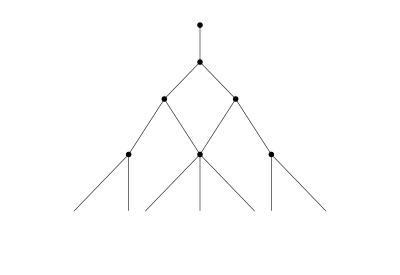

```mathematica
BratteliDiagramSn[4,Output->Graph]
```

### 6. Dimension of irreducible representation of GL(N), O(N), Sp(N)

```mathematica
?DimOfIrrep
```

```mathematica
$LieGroups
```

{GeneralLinearGroup,OrthogonalGroup,SymplecticGroup}

```mathematica
{GeneralLinearGroup[d],OrthogonalGroup[d],SymplecticGroup[d]}
```

{UnderBar[GL][d],O̲[d],UnderBar[Sp][d]}

```mathematica
IntegerPartitions[4]
DimOfIrrep[#,UnderBar[GL][N]]&/@%
```

{{4},{3,1},{2,2},{2,1,1},{1,1,1,1}}

{1/24 N (1+N) (2+N) (3+N),1/8 (-1+N) N (1+N) (2+N),1/12 (-1+N) N^2 (1+N),1/8 (-2+N) (-1+N) N (1+N),1/24 (-3+N) (-2+N) (-1+N) N}

```mathematica
IntegerPartitions[4]
DimOfIrrep[#,O̲[N]]&/@%
```

{{4},{3,1},{2,2},{2,1,1},{1,1,1,1}}

{1/24 (-1+N) N (1+N) (6+N),1/8 (-2+N) (-1+N) (1+N) (4+N),1/12 (-3+N) N (1+N) (2+N),1/8 (-3+N) (-1+N) N (2+N),1/24 (-3+N) (-2+N) (-1+N) N}

```mathematica
IntegerPartitions[4]
DimOfIrrep[#,UnderBar[Sp][N]]&/@%
```

{{4},{3,1},{2,2},{2,1,1},{1,1,1,1}}

{1/24 N (1+N) (2+N) (3+N),1/8 (-2+N) N (1+N) (3+N),1/12 (-2+N) (-1+N) N (3+N),1/8 (-4+N) (-1+N) (1+N) (2+N),1/24 (-6+N) (-1+N) N (1+N)}

### 7. Branching rules GL(N) -> O(N) , GL(N)->Sp(N)

```mathematica
BranchingRule[{2,2},GeneralLinearGroup,OrthogonalGroup]
```

{{},{2},{2,2}}

```mathematica
LittlewoodRichardsonRule[{1,1},{1},{1}]
```

{{2,2},{3,1},{2,1,1},{2,1,1},{1,1,1,1}}

```mathematica
BranchingRule[#,GeneralLinearGroup,OrthogonalGroup]&/@LittlewoodRichardsonRule[{1,1},{1},{1}]
SortBy[Flatten[%,1],Tr[#]&]
```

{{{},{2},{2,2}},{{2},{1,1},{3,1}},{{1,1},{2,1,1}},{{1,1},{2,1,1}},{{1,1,1,1}}}

{{},{2},{2},{1,1},{1,1},{1,1},{2,2},{3,1},{2,1,1},{2,1,1},{1,1,1,1}}

```mathematica
NewellLittlewoodRule[{1,1},{1},{1}]
```

{{},{2},{2},{1,1},{1,1},{1,1},{2,2},{3,1},{2,1,1},{2,1,1},{1,1,1,1}}

```mathematica
BranchingRule[{3,1},GeneralLinearGroup,OrthogonalGroup]
BranchingRule[{2,1,1},GeneralLinearGroup,OrthogonalGroup]
BranchingRule[{1,1,1,1},GeneralLinearGroup,OrthogonalGroup]
```

{{2},{1,1},{3,1}}

{{1,1},{2,1,1}}

{{1,1,1,1}}

```mathematica
BranchingRule[{3,1},GeneralLinearGroup[4],OrthogonalGroup[4]]
```

{{2},{1,1},{3,1}}

```mathematica
BranchingRule[{2,2},GeneralLinearGroup,OrthogonalGroup]
```

{{},{2},{2,2}}

```mathematica
BranchingRule[{2,2},GeneralLinearGroup[4],OrthogonalGroup[4]]
```

{{},{2},{2,2}}

```mathematica
BranchingRule[{2,2},GeneralLinearGroup[3],OrthogonalGroup[3]]
BranchingRule[{2,2},GeneralLinearGroup[2],OrthogonalGroup[2]]
BranchingRule[{2,2},GeneralLinearGroup[1],OrthogonalGroup[1]]
```

{{},{2}}

{{},{2}}

BranchingRule::GLrestriction: The number of raws in {2,2} is greater than 1.

Throw::nocatch: Uncaught Throw[Null] returned to top level.

Hold[Throw[Null]]